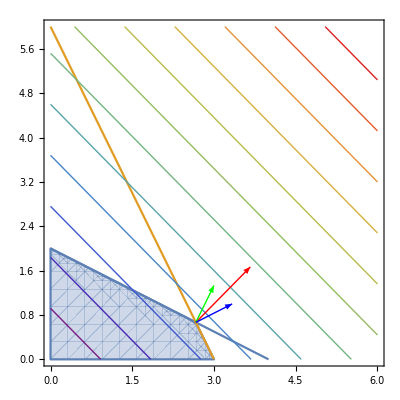

```mathematica
Show[RegionPlot[(x+2*y≤4)&&(2*x+y≤6)&&(x≥0)&&(y≥0),{x,0,6},{y,0,6}],
ContourPlot[{x+2*y==4,2*x+y==6,x==0,y==0},{x,0,6},{y,0,6}],
ContourPlot[x+y,{x,0,6},{y,0,6},ContourShading->None,Contours->12,ContourStyle->Table[{ColorData["Rainbow",(i-1)/(12-1)]},{i,12}]],
Graphics[{Red,Arrow[{{8/3,2/3},({8/3,2/3} + {1,1})}]}],
Graphics[{Green,Arrow[{{8/3,2/3},({8/3,2/3} + (1/3)*{1,2})}]}],
Graphics[{Blue,Arrow[{{8/3,2/3},({8/3,2/3} + (1/3)*{2,1})}]}]]
```

```mathematica
Solve[{x+2*y==4,2*x+y==6},{x,y}]
```

{{x→8/3,y→2/3}}

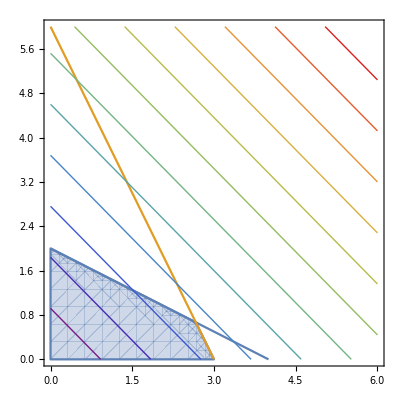

```mathematica
Show[RegionPlot[(x+2*y≤4)&&(2*x+y≤6)&&(x≥0)&&(y≥0),{x,0,6},{y,0,6}],
ContourPlot[{x+2*y==4,2*x+y==6,x==0,y==0},{x,0,6},{y,0,6}],
ContourPlot[x+y,{x,0,6},{y,0,6},ContourShading->None,Contours->12,ContourStyle->Table[{ColorData["Rainbow",(i-1)/(12-1)]},{i,12}]]]
```

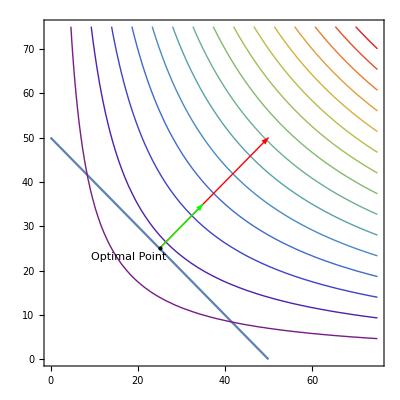

```mathematica
Show[
ContourPlot[2*x+2*y==100,{x,0,75},{y,0,75}],
ContourPlot[x*y,{x,0,75},{y,0,75},ContourShading->None,Contours->15,ContourStyle->Table[{ColorData["Rainbow",(i-1)/(15-1)]},{i,15}]],
Graphics[{Red,Arrow[{{25,25},({25,25} + 1*{25,25})}]}],
Graphics[{Green,Arrow[{{25,25},({25,25} + (25/5)*{2,2})}]}],
Graphics[Point[{25,25}]],Graphics[Text["Optimal Point", {18,23}]]
]
```